# NFL Players Heights VS Weights VS Position

## Load Data

```mathematica
SetDirectory[NotebookDirectory[]];
rawData=Import["NFL.csv"];
{header,data}={rawData[[1]],rawData[[2;;All]]};
```

```mathematica
position=Position[header,"Position"][[1,1]];
weight=Position[header,"Weight (lbs)"][[1,1]];
height=Position[header,"Height (inches)"][[1,1]];
```

```mathematica
positionsID=((data[[All,position]]//DeleteDuplicates)//Sort)[[2;;All]]
```

{C,CB,DB,DE,DL,DT,FB,FS,G,ILB,K,LB,LS,MLB,NT,OG,OL,OLB,OT,P,QB,RB,SAF,SS,T,TE,WR}

## Initial Draft

```mathematica
positions=data[[All,position]];
weights=data[[All,weight]]*0.453592;
heights=data[[All,height]]*0.0254;
```

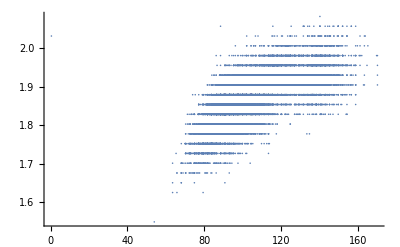

```mathematica
ListPlot[{weights,heights}//Transpose]
```

## Trying transposing the data

```mathematica
triplets=Transpose[{heights,weights,positions}];
filtered=Cases[triplets,{a_,b_,c_}/;StringLength[c]≥1];
```

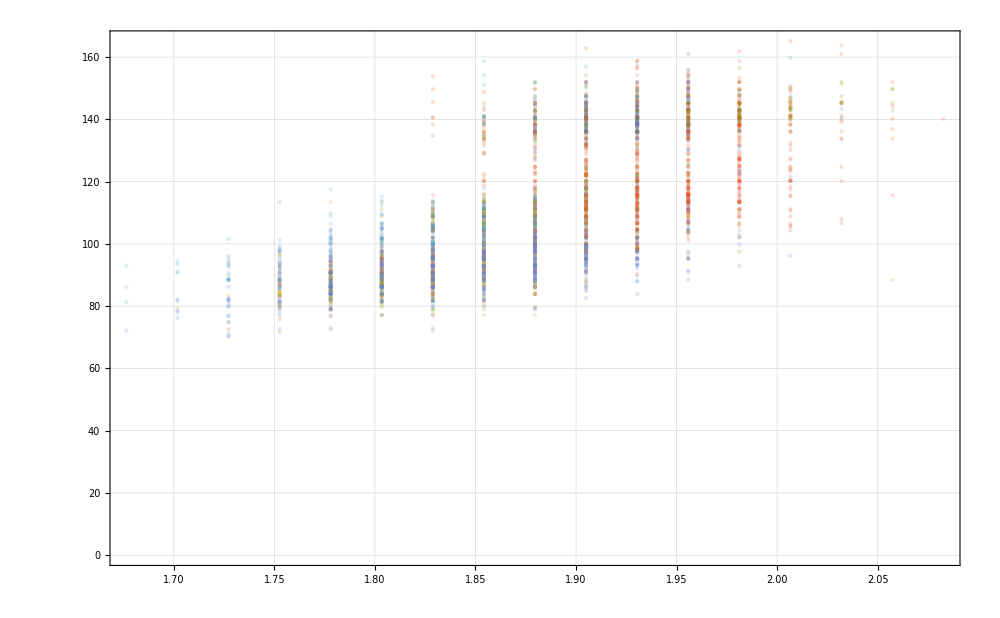

```mathematica
clustered=Map[Cases[filtered,{a_,b_,#}->{a,b}]&,positionsID];
ListPlot[clustered
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->18
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Opacity[.15]]
,ImageSize->1000
,PlotStyle->Directive[PointSize[Large],Opacity[.2]]
]
```

## Manual Clustering of Positions

```mathematica
clusteredIDs={{"C","LS","OG","OT","NT","T","G","OL","DL","DT","DE"},{"DB","CB","OLB","SAF","SS","FS"},{"K","P"},{"ILB","LB","MLB"},{"QB"},{"RB","FB"},{"TE"},{"WR"}}
```

{{C,LS,OG,OT,NT,T,G,OL,DL,DT,DE},{DB,CB,OLB,SAF,SS,FS},{K,P},{ILB,LB,MLB},{QB},{RB,FB},{TE},{WR}}

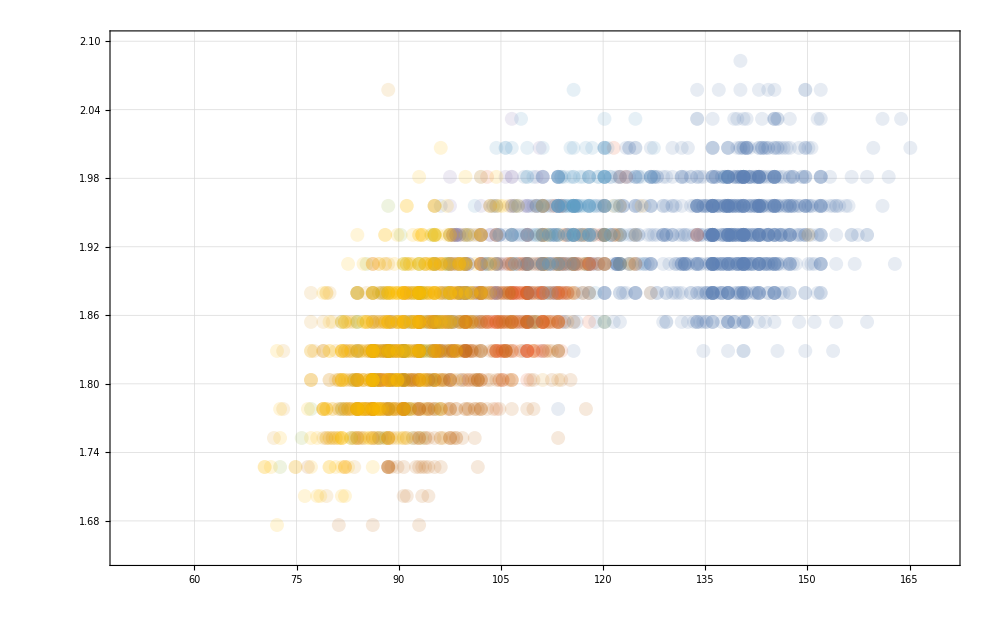

```mathematica
clustered=Map[Cases[filtered,{a_,b_,c_}/;MemberQ[#,c]->{b,a+RandomReal[{-0,0}]}]&,clusteredIDs];
base=ListPlot[clustered
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->18
,ColorFunction->"BrightBands"
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Opacity[.15]]
,ImageSize->1000
,PlotRange->{{50,170},{1.65,2.1}}
,PlotLegends->{"Line","DB","K","LB","QB","RB","TE","WR"}
,PlotStyle->Directive[PointSize[.01],Opacity[.15]]
]
```

## Highlighting a cluster

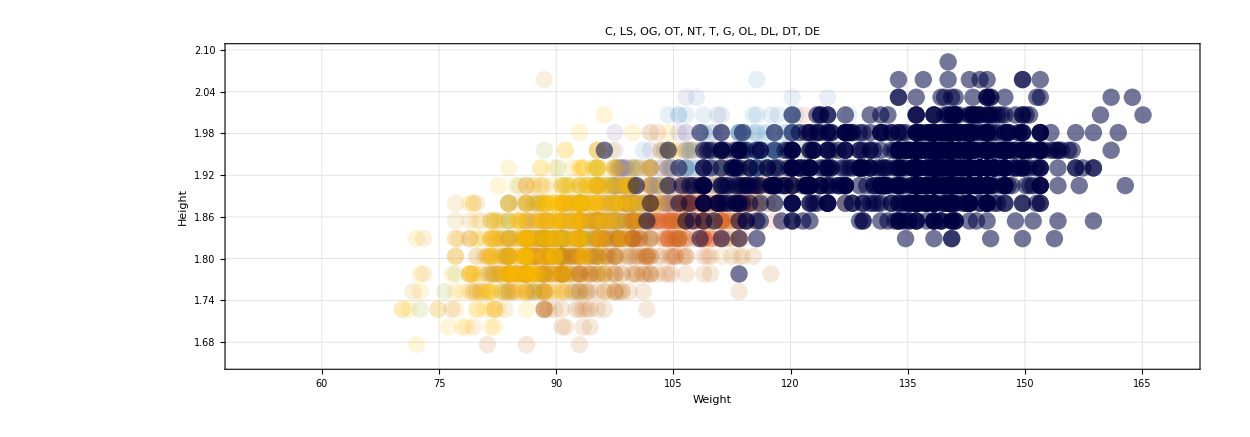

```mathematica
index=1;
clustered=Map[Cases[filtered,{a_,b_,c_}/;MemberQ[#,c]->{b,a}]&,{clusteredIDs[[index]]}];
layer=ListPlot[clustered
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->18
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Opacity[.15]]
,ImageSize->1000
,PlotRange->{{50,170},{1.6,2.1}}
,PlotStyle->Directive[PointSize[.01],Darker[Blue,.75],Opacity[.5]]
];
Show[base,layer
,AspectRatio->.35
,FrameLabel->(Style[#,40]&/@{"Weight","Height"})
,ImageSize->1250
,PlotLabel->(StringDelete[ToString[clusteredIDs[[index]]],{"{","}"}]//Style[#,50]&)
]
```

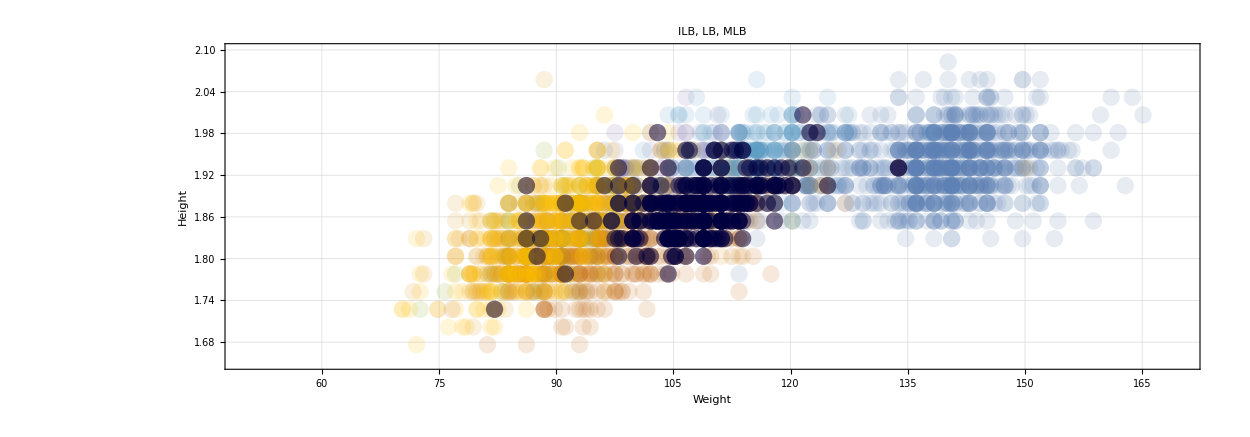

```mathematica
index=4;
clustered=Map[Cases[filtered,{a_,b_,c_}/;MemberQ[#,c]->{b,a}]&,{clusteredIDs[[index]]}];
layer=ListPlot[clustered
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->18
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Opacity[.15]]
,ImageSize->1000
,PlotRange->{{50,170},{1.6,2.1}}
,PlotStyle->Directive[PointSize[.01],Darker[Blue,.75],Opacity[.5]]
];
Show[base,layer
,AspectRatio->.35
,FrameLabel->(Style[#,40]&/@{"Weight","Height"})
,ImageSize->1250
,PlotLabel->(StringDelete[ToString[clusteredIDs[[index]]],{"{","}"}]//Style[#,50]&)
]
```

## Improving Aesthetics

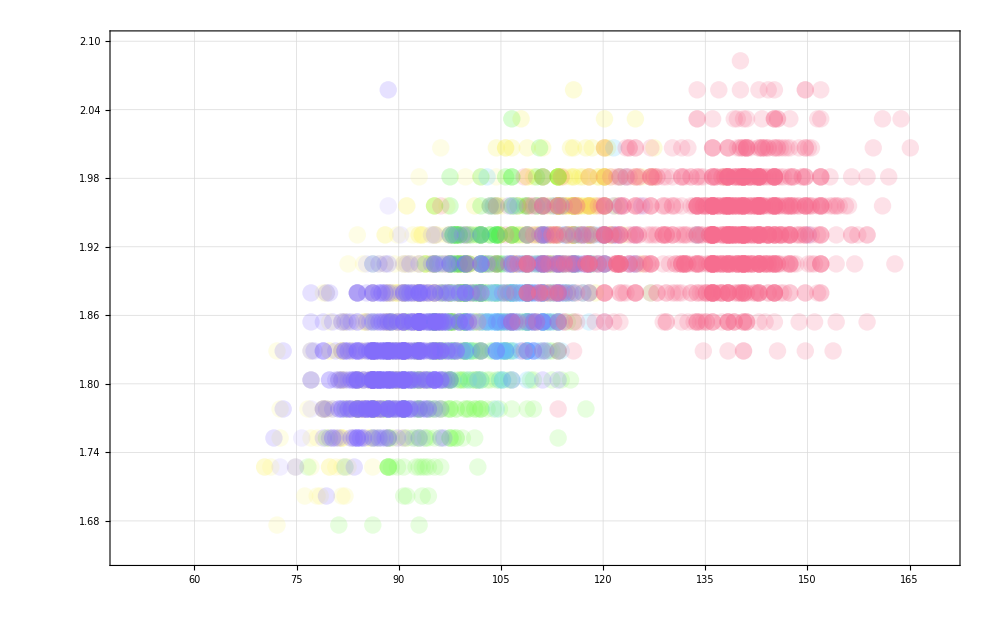

```mathematica
clustered=Map[Cases[filtered,{a_,b_,c_}/;MemberQ[#,c]->{b,a+RandomReal[{-0,0}]}]&,clusteredIDs];
colors=ColorData["BrightBands"][#/10]&/@Range[clusteredIDs//Length];
base=Table[ListPlot[clustered[[i]]
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->18
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Opacity[.15]]
,ImageSize->1000
,PlotRange->{{50,170},{1.65,2.1}}
,PlotStyle->Directive[colors[[i]],PointSize[.0125],Opacity[.2]]
]
,{i,1,clustered//Length}]//Reverse//Show
```

## Putting it all together

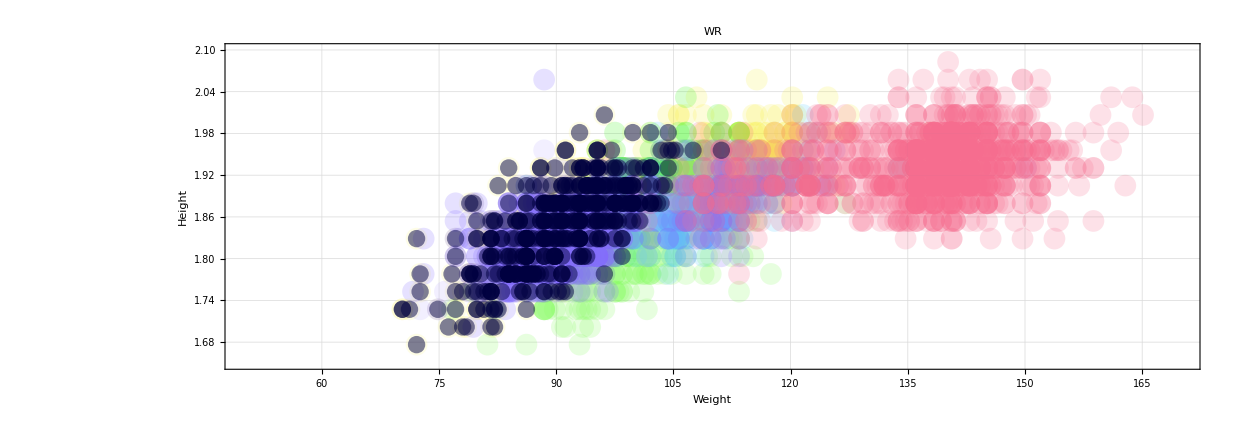
-Graphics- |

NFL08.png

```mathematica
index=8;
clustered=Map[Cases[filtered,{a_,b_,c_}/;MemberQ[#,c]->{b,a}]&,{clusteredIDs[[index]]}];
layer=ListPlot[clustered
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->18
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Opacity[.15]]
,ImageSize->1000
,PlotRange->{{50,170},{1.6,2.1}}
,PlotStyle->Directive[PointSize[.01],Darker[Blue,.75],Opacity[.5]]
];
swatch=SwatchLegend[colors,{"Line","DB","K","LB","QB","RB","TE","WR"},LegendMarkerSize->30,LabelStyle->20];
grid=Grid[{{
Show[base,layer
,AspectRatio->.35
,FrameLabel->(Style[#,40]&/@{"Weight","Height"})
,ImageSize->1250
,PlotLabel->(StringDelete[ToString[clusteredIDs[[index]]],{"{","}"}]//Style[#,50]&)
]
,
swatch
}}]
Export["NFL0"<>ToString[index]<>".png",grid,ImageSize->2500,ImageResolution->300]
```